```mathematica
(* source: http://mathgis.blogspot.com *)
```

```mathematica
peaks[x_,y_]:=3*(1-x)^2.*Exp[-(x^2)-(y+1)^2]-10*(x/5-x^3-y^5) Exp[-x^2-y^2]-1/3Exp[-(x+1)^2-y^2];
```

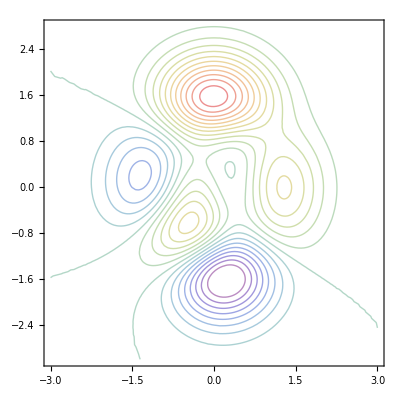

```mathematica
(* number of contour lines *)
numC=20;
cplt=ContourPlot[peaks[x,y],{x,-3,3},{y,-3,3},PlotRange->All,ContourShading->None,ContourStyle->Table[{ColorData["Rainbow",(i-1)/(numC-1)]},{i,numC}],Contours->numC]
```

```mathematica
peaksplt=Plot3D[peaks[x,y],{x,-3,3},{y,-3,3},PlotRange->All,BoxRatios->{1,1,0.8}, Mesh->None,MeshFunctions->(#3&),ColorFunction->"Rainbow",BoundaryStyle->None]
```

-Graphics3D-

```mathematica
(* turn contourplot into 3D *)
c3d=Graphics[cplt][[1]];
c3dplt=Graphics3D[c3d,BoxRatios->1]/.{x_?AtomQ,y_?AtomQ}:>{x,y,peaks[x,y]}
```

-Graphics3D-

```mathematica
Show[peaksplt,c3dplt]
```

-Graphics3D-

```mathematica
c3dplt=Graphics3D[c3d,BoxRatios->1]/.{x_?AtomQ,y_?AtomQ}:>{x,y,-10}
```

-Graphics3D-

```mathematica
Show[peaksplt,c3dplt]
```

-Graphics3D-